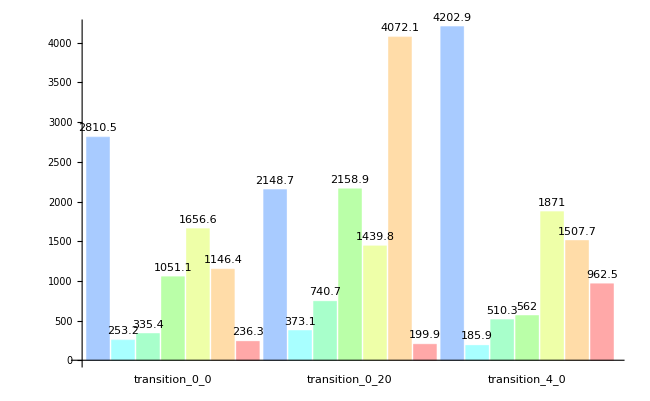
-Graphics--Graphics- | cryptominisat(jni)
-Graphics- | glucose(jni)
-Graphics- | minisat(jni)
-Graphics- | sat4j
-Graphics- | lingeling(jni)
-Graphics- | plingeling(jni)
-Graphics- | minisatprover(jni)

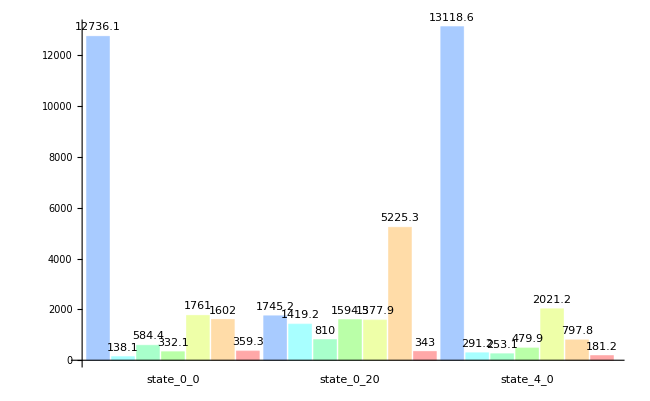
-Graphics--Graphics- | cryptominisat(jni)
-Graphics- | glucose(jni)
-Graphics- | minisat(jni)
-Graphics- | sat4j
-Graphics- | lingeling(jni)
-Graphics- | plingeling(jni)
-Graphics- | minisatprover(jni)

```mathematica
simple=Import["/home/chef/Egyetem/Onlab1/msc-thesis/measurements/simple_alloyoptions_2_aggregated.csv","table",FieldSeparators->";"];
labels1=simple[[2;;4, 1]];
values1=simple[[2;;4,2;;8]];
labels2=simple[[5;;7, 1]];
values2=simple[[5;;7,2;;8]];
legends=simple[[1, 2;;8]];
simple1=BarChart[values1,ChartLabels->{labels1,None}, ChartLegends -> legends,LabelingFunction->(Placed[#,Above]&), ImageSize -> 650]
simple2=BarChart[values2,ChartLabels->{labels2,None}, ChartLegends -> legends,LabelingFunction->(Placed[#,Above]&), ImageSize -> 650]
Export["/home/chef/Egyetem/Onlab1/msc-thesis/measurements/options_transition.png", simple1];
Export["/home/chef/Egyetem/Onlab1/msc-thesis/measurements/options_state.png", simple2];
```

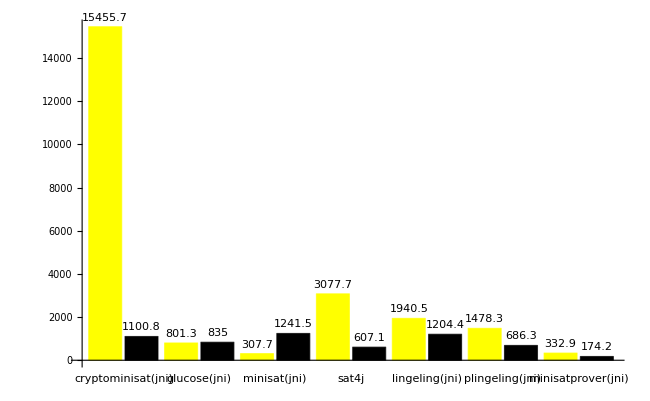
-Graphics--Graphics- | Original
-Graphics- | Optimized

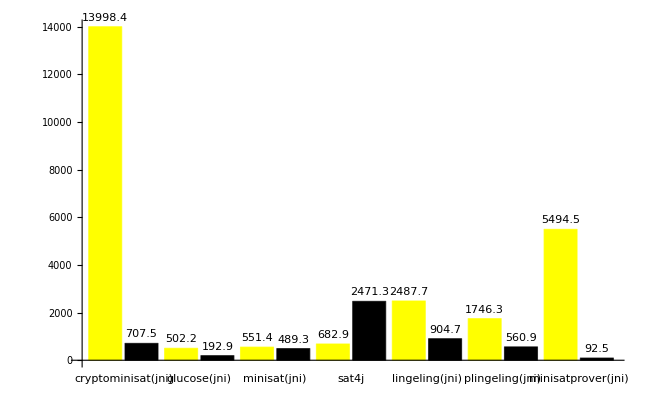
-Graphics--Graphics- | Original
-Graphics- | Optimized

```mathematica
optimalizations=Import["/home/chef/Egyetem/Onlab1/msc-thesis/measurements/optimalizations_aggregated.csv","table",FieldSeparators->";"];
values1={};
Do[values1=Append[values1, optimalizations[[2;;3,i]]],{i,2,8}]
values2={};
Do[values2=Append[values2, optimalizations[[5;;6,i]]],{i,2,8}]
labels =optimalizations[[1,2;;8]];
legends = {"Original", "Optimized"};
optimalization1=BarChart[values1,ChartLabels->{labels,None}, ChartLegends -> legends,LabelingFunction->(Placed[#,Above]&),ChartStyle -> {Yellow, Black}, ImageSize -> 650]
optimalization2=BarChart[values2,ChartLabels->{labels,None}, ChartLegends -> legends,LabelingFunction->(Placed[#,Above]&),ChartStyle -> {Yellow, Black}, ImageSize -> 650]
Export["/home/chef/Egyetem/Onlab1/msc-thesis/measurements/optimalization_state.png", optimalization1];
Export["/home/chef/Egyetem/Onlab1/msc-thesis/measurements/optimalization_transition.png", optimalization2];
```

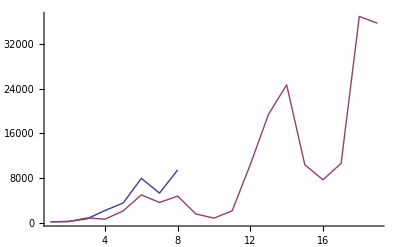

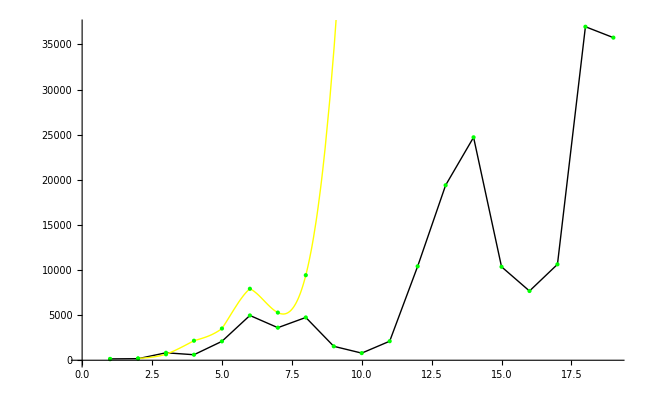

```mathematica
scalabilitystate=Import["/home/chef/Egyetem/Onlab1/msc-thesis/measurements/scalability_state_aggregated.csv","table",FieldSeparators->";"];
values1=scalabilitystate[[2]];
scalabilitytransition=Import["/home/chef/Egyetem/Onlab1/msc-thesis/measurements/scalability_transition_aggregated.csv","table",FieldSeparators->";"];
values2=scalabilitytransition[[2]];
legends={"states","transitions"};
ListLinePlot[{values1, values2}, PlotRange -> All]
f1=ListInterpolation[values1];
states=Plot[f1[x],{x,2,10}, PlotStyle -> {Yellow, Thick}];
transitions=ListLinePlot[values2, PlotStyle -> {Black, Thick}];
scalability=Show[transitions, states,ListPlot[{values1, values2},PlotStyle -> {{Green, PointSize[Large]},{Green, PointSize[Large]}}], ImageSize -> 650]
Export["/home/chef/Egyetem/Onlab1/msc-thesis/measurements/scalability.png", scalability];
```